Figure 1

```mathematica
cellCoordinates2D=Flatten[Table[{x,y},{x,0,1,1/10},{y,0,1,1/10}],1];
polarCellCo2D={N@√((#[[1]])^2+(#[[2]])^2),If[#[[1]]==0,0,ArcTan[N@((#[[2]])/(#[[1]]))]]}&/@Select[Flatten[Table[{x,y},{x,0,1,1/15},{y,0,1,1/15}],1],#[[2]]+√3#[[1]]≤ √3&&#[[2]]-1/(√3)#[[1]]≤ 0&];
```

```mathematica
ω1=1;ω2=1;ω3=1;
res1C=NMaximize[{(Sum[(10-((1-g1[x])^2+(g2[x])^2+(g3[x])^2)),{x,cellCoordinates2D}])^ω1(Sum[(10-((g1[x])^2+(1-g2[x])^2+(g3[x])^2)),{x,cellCoordinates2D}])^ω2(Sum[(10-((g1[x])^2+(g2[x])^2+(1-g3[x])^2)),{x,cellCoordinates2D}])^ω3
,And@@(#>0&/@Flatten[Table[{g1[x],g2[x],g3[x]},{x,cellCoordinates2D}]])},Flatten[Table[{g1[x],g2[x],g3[x]},{x,cellCoordinates2D}]]];
```

```mathematica
res1C[[1]]
```

1.44034×10^9

```mathematica
tri1C=PrincipalComponents[Join[Chop[Table[{g1[x],g2[x],g3[x]},{x,cellCoordinates2D}]/.res1C[[2]],10^-2],{{1,0,0},{0,1,0},{0,0,1}}]][[;;,;;2]];
```

```mathematica
geneExp1C=Join[Chop[Table[{g1[x],g2[x],g3[x]},{x,cellCoordinates2D}]/.res1C[[2]],10^-2],{{1,0,0},{0,1,0},{0,0,1}}];
```

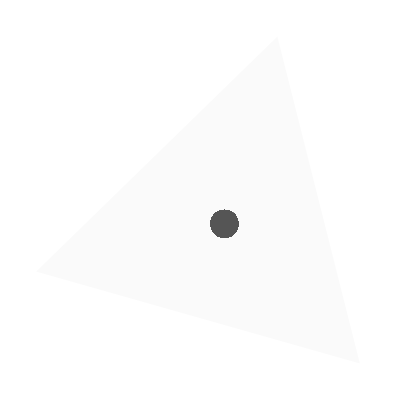

```mathematica
Show[Graphics[{Opacity[0.02],Simplex[tri1C[[-3;;]]]},Frame->False],Graphics[Flatten[{PointSize[.05],{Blend[{Red,Blue,Green},#[[2]]],Point[#[[1]]]}&/@({tri1C[[;;-4]],geneExp1C[[;;-4]]}ᵀ)}],AspectRatio->Automatic,Frame->False],PlotRange->All]
```

```mathematica
a=1;b=1;c=1;d=1;ω1=1;ω2=1;ω3=1;
res1E=NMaximize[{(Sum[(ⅇ^(-2 √((1-g1[x])^2+(g2[x])^2+(g3[x])^2))),{x,cellCoordinates2D[[;;30]]}])^ω1(Sum[(ⅇ^(-2 √((g1[x])^2+(1-g2[x])^2+(g3[x])^2))),{x,cellCoordinates2D[[;;30]]}])^ω2(Sum[(ⅇ^(-2 √((g1[x])^2+(g2[x])^2+(1-g3[x])^2))),{x,cellCoordinates2D[[;;30]]}])^ω3
,And@@(#>0&/@Flatten[Table[{g1[x],g2[x],g3[x]},{x,cellCoordinates2D[[;;30]]}]])},Flatten[Table[{g1[x],g2[x],g3[x]},{x,cellCoordinates2D[[;;30]]}]]];
```

```mathematica
res1E[[1]]
```

1358.61

```mathematica
tri1E=PrincipalComponents[Join[Chop[Table[{g1[x],g2[x],g3[x]},{x,cellCoordinates2D[[;;30]]}]/.res1E[[2]],10^-2],{{1,0,0},{0,1,0},{0,0,1}}]][[;;,;;2]];
```

```mathematica
geneExp1E=Join[Chop[Table[{g1[x],g2[x],g3[x]},{x,cellCoordinates2D[[;;30]]}]/.res1E[[2]],10^-2],{{1,0,0},{0,1,0},{0,0,1}}];
```

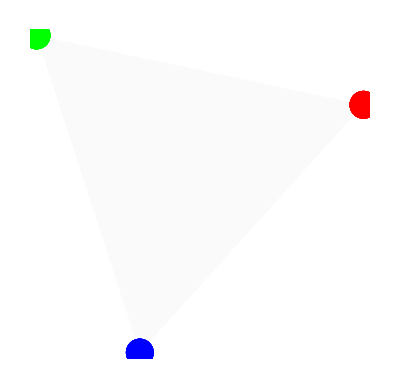

```mathematica
Show[Graphics[{Opacity[0.02],Simplex[tri1E[[-3;;]]]},Frame->False],Graphics[Flatten[{PointSize[.05],{Blend[{Red,Blue,Green},#[[2]]],Point[#[[1]]]}&/@({tri1E[[;;-4]],geneExp1E[[;;-4]]}ᵀ)}],AspectRatio->Automatic,Frame->False],PlotRange->All]
```

```mathematica
a=1;b=1;c=1;d=1;ω1=1;ω2=1;ω3=1;
res1H=NMaximize[{(Sum[(10-√((1-g1[x])^2+(g2[x])^2+(g3[x])^2))(.01+a x[[1]]),{x,polarCellCo2D[[;;]]}])^ω1(Sum[(10-√((g1[x])^2+(1-g2[x])^2+(g3[x])^2))(1-b x[[1]]),{x,polarCellCo2D[[;;]]}])^ω2(Sum[(10-√((g1[x])^2+(g2[x])^2+(1-g3[x])^2)),{x,polarCellCo2D[[;;]]}])^ω3
,And@@(#>0&/@Flatten[Table[{g1[x],g2[x],g3[x]},{x,polarCellCo2D[[;;]]}]])},Flatten[Table[{g1[x],g2[x],g3[x]},{x,polarCellCo2D[[;;]]}]]];
```

```mathematica
res1H[[1]]
```

3.82487×10^7

```mathematica
tri1H=PrincipalComponents[Join[Chop[Table[{g1[x],g2[x],g3[x]},{x,polarCellCo2D[[;;]]}]/.res1H[[2]],10^-2],{{1,0,0},{0,1,0},{0,0,1}}]][[;;,;;2]];
```

```mathematica
geneExp1H=Join[Chop[Table[{g1[x],g2[x],g3[x]},{x,polarCellCo2D[[;;]]}]/.res1H[[2]],10^-2],{{1,0,0},{0,1,0},{0,0,1}}];
```

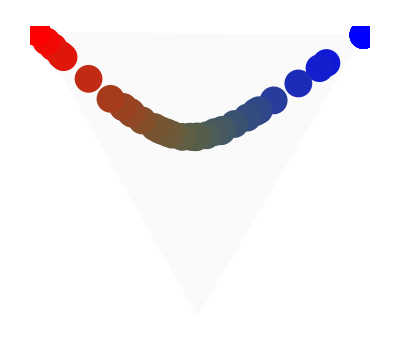

```mathematica
Show[Graphics[{Opacity[0.02],Simplex[tri1H[[-3;;]]]},Frame->False],Graphics[Flatten[{PointSize[.05],{Blend[{Red,Blue,Green},#[[2]]],Point[#[[1]]]}&/@({tri1H[[;;-4]],geneExp1H[[;;-4]]}ᵀ)}],AspectRatio->Automatic,Frame->False],PlotRange->All]
```

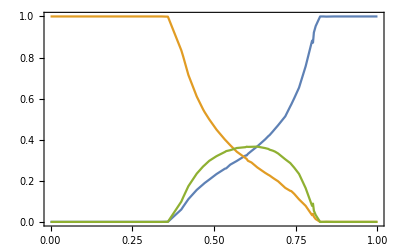

```mathematica
ListLinePlot[Mean/@GatherBy[Sort[#],First]&/@Evaluate[{Table[{x[[1]],g1[x]},{x,polarCellCo2D}],Table[{x[[1]],g2[x]},{x,polarCellCo2D}],Table[{x[[1]],g3[x]},{x,polarCellCo2D}]}/.res1H[[2]]],PlotRange->All,AxesOrigin->{0,0},Axes->False,Frame->True]
```

```mathematica
a=1;b=1;c=1;d=1;ω1=1;ω2=1;ω3=1;
res1K=NMaximize[{(Sum[(10-√((1-g1[x])^2+(g2[x])^2+(g3[x])^2))(1-a x[[1]]),{x,cellCoordinates2D}])^ω1(Sum[(10-√((g1[x])^2+(1-g2[x])^2+(g3[x])^2))(1-b x[[2]]),{x,cellCoordinates2D}])^ω2(Sum[(10-√((g1[x])^2+(g2[x])^2+(1-g3[x])^2)),{x,cellCoordinates2D}])^ω3
,And@@(#>0&/@Flatten[Table[{g1[x],g2[x],g3[x]},{x,cellCoordinates2D}]])(*&&And@@(#<ϵ&/@Flatten[Differences/@(Table[{g1[x],g2[x],g3[x]},{x,0,1,1/n}]ᵀ)])*)},Flatten[Table[{g1[x],g2[x],g3[x]},{x,cellCoordinates2D}]]];
```

```mathematica
tri1K=PrincipalComponents[Join[Chop[Table[{g1[x],g2[x],g3[x]},{x,cellCoordinates2D}]/.res1K[[2]],10^-2],{{1,0,0},{0,1,0},{0,0,1}}]][[;;,;;2]];
```

```mathematica
geneExp1K=Join[Chop[Table[{g1[x],g2[x],g3[x]},{x,cellCoordinates2D}]/.res1K[[2]],10^-2],{{1,0,0},{0,1,0},{0,0,1}}];
```

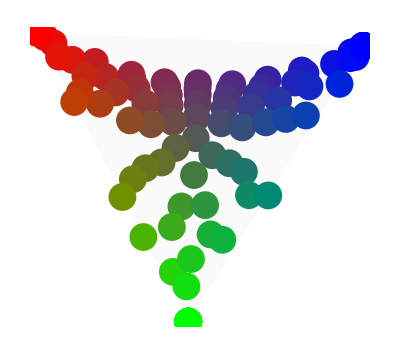

```mathematica
Show[Graphics[{Opacity[0.02],Simplex[tri1K[[-3;;]]]},Frame->False],Graphics[Flatten[{PointSize[.05],{Blend[{Red,Blue,Green},#[[2]]],Point[#[[1]]]}&/@({tri1K[[;;-4]],geneExp1K[[;;-4]]}ᵀ)}],AspectRatio->Automatic,Frame->False],PlotRange->All]
```

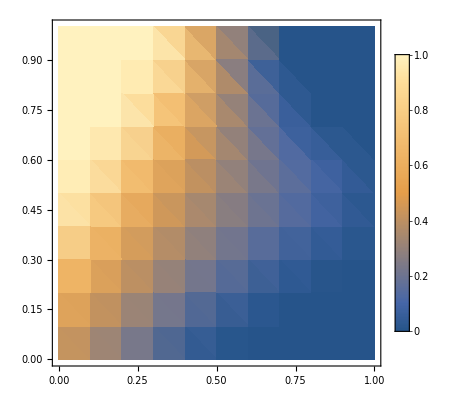
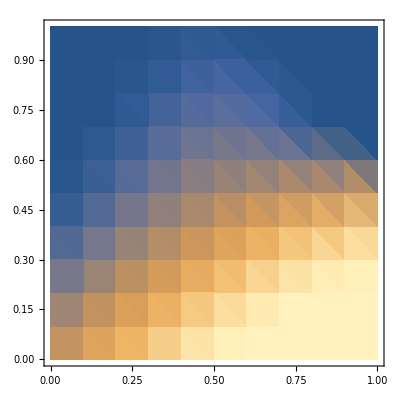
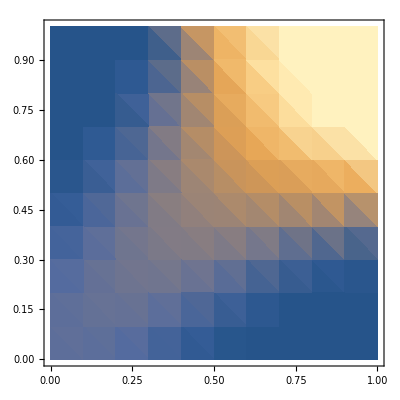

```mathematica
{ListDensityPlot[Append[#[[1]],#[[2]]]&/@({cellCoordinates2D,geneExp1K[[;;-4,1]]}ᵀ),PlotLegends->Automatic],ListDensityPlot[Append[#[[1]],#[[2]]]&/@({cellCoordinates2D,geneExp1K[[;;-4,2]]}ᵀ)],ListDensityPlot[Append[#[[1]],#[[2]]]&/@({cellCoordinates2D,geneExp1K[[;;-4,3]]}ᵀ)]}
```

```mathematica
a=1;b=1;c=1;d=1;ω1=1;ω2=1;ω3=1;
resS1B1=NMaximize[{(Sum[(10-((1-g1[x])^2+(g2[x])^2+(g3[x])^2))(0.01+a x[[1]]),{x,cellCoordinates2D}])^ω1(Sum[(10-((g1[x])^2+(1-g2[x])^2+(g3[x])^2))(1-b x[[1]]),{x,cellCoordinates2D}])^ω2(Sum[(10-((g1[x])^2+(g2[x])^2+(1-g3[x])^2)),{x,cellCoordinates2D}])^ω3
,And@@(#>0&/@Flatten[Table[{g1[x],g2[x],g3[x]},{x,cellCoordinates2D}]])(*&&And@@(#<ϵ&/@Flatten[Differences/@(Table[{g1[x],g2[x],g3[x]},{x,0,1,1/n}]ᵀ)])*)},Flatten[Table[{g1[x],g2[x],g3[x]},{x,cellCoordinates2D}]]];
```

```mathematica
resS1B1[[1]]
```

3.77584×10^8

```mathematica
triS1B1=PrincipalComponents[Join[Chop[Table[{g1[x],g2[x],g3[x]},{x,cellCoordinates2D}]/.resS1B1[[2]],10^-2],{{1,0,0},{0,1,0},{0,0,1}}]][[;;,;;2]];
```

```mathematica
geneExpS1B1=Join[Chop[Table[{g1[x],g2[x],g3[x]},{x,cellCoordinates2D}]/.resS1B1[[2]],10^-2],{{1,0,0},{0,1,0},{0,0,1}}];
```

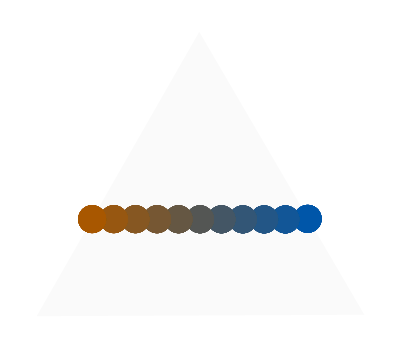

```mathematica
Show[Graphics[{Opacity[0.02],Simplex[triS1B1[[-3;;]]]},Frame->False],Graphics[Flatten[{PointSize[.05],{Blend[{Red,Blue,Green},#[[2]]],Point[#[[1]]]}&/@({triS1B1[[;;-4]],geneExpS1B1[[;;-4]]}ᵀ)}],AspectRatio->Automatic,Frame->False],PlotRange->All]
```

```mathematica
a=1;b=1;c=1;d=1;ω1=1;ω2=1;ω3=1;
resS1B2=NMaximize[{(Sum[(10-((1-g1[x])^2+(g2[x])^2+(g3[x])^2))(1-a x[[1]]),{x,cellCoordinates2D}])^ω1(Sum[(10-((g1[x])^2+(1-g2[x])^2+(g3[x])^2))(1-b x[[2]]),{x,cellCoordinates2D}])^ω2(Sum[(10-((g1[x])^2+(g2[x])^2+(1-g3[x])^2)),{x,cellCoordinates2D}])^ω3
,And@@(#>0&/@Flatten[Table[{g1[x],g2[x],g3[x]},{x,cellCoordinates2D}]])(*&&And@@(#<ϵ&/@Flatten[Differences/@(Table[{g1[x],g2[x],g3[x]},{x,0,1,1/n}]ᵀ)])*)},Flatten[Table[{g1[x],g2[x],g3[x]},{x,cellCoordinates2D}]]];
```

```mathematica
resS1B2[[1]]
```

3.67707×10^8

```mathematica
triS1B2=PrincipalComponents[Join[Chop[Table[{g1[x],g2[x],g3[x]},{x,cellCoordinates2D}]/.resS1B2[[2]],10^-2],{{1,0,0},{0,1,0},{0,0,1}}]][[;;,;;2]];
```

```mathematica
geneExpS1B2=Join[Chop[Table[{g1[x],g2[x],g3[x]},{x,cellCoordinates2D}]/.resS1B2[[2]],10^-2],{{1,0,0},{0,1,0},{0,0,1}}];
```

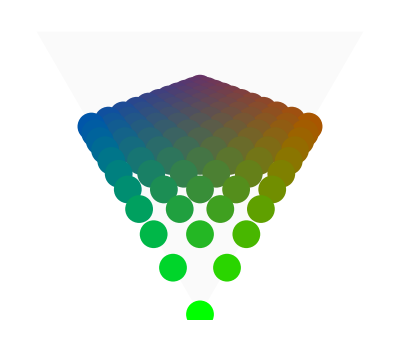

```mathematica
Show[Graphics[{Opacity[0.02],Simplex[triS1B2[[-3;;]]]},Frame->False],Graphics[Flatten[{PointSize[.05],{Blend[{Red,Blue,Green},#[[2]]],Point[#[[1]]]}&/@({triS1B2[[;;-4]],geneExpS1B2[[;;-4]]}ᵀ)}],AspectRatio->Automatic,Frame->False],PlotRange->All]
```

```mathematica
a=1;b=1;c=1;d=1;ω1=1;ω2=1;ω3=1;
resS1C1=NMaximize[{(Sum[(ⅇ^(-√((1-g1[x])^2+(g2[x])^2+(g3[x])^2)))(0.01+a x[[1]]),{x,cellCoordinates2D}])^ω1(Sum[(ⅇ^(-√((g1[x])^2+(1-g2[x])^2+(g3[x])^2)))(1-b x[[1]]),{x,cellCoordinates2D}])^ω2(Sum[(ⅇ^(-√((g1[x])^2+(g2[x])^2+(1-g3[x])^2))),{x,cellCoordinates2D}])^ω3
,And@@(#>0&/@Flatten[Table[{g1[x],g2[x],g3[x]},{x,cellCoordinates2D}]])(*&&And@@(#<ϵ&/@Flatten[Differences/@(Table[{g1[x],g2[x],g3[x]},{x,0,1,1/n}]ᵀ)])*)},Flatten[Table[{g1[x],g2[x],g3[x]},{x,cellCoordinates2D}]]];
```

```mathematica
resS1C1[[1]]
```

97047.

```mathematica
triS1C1=PrincipalComponents[Join[Chop[Table[{g1[x],g2[x],g3[x]},{x,cellCoordinates2D}]/.resS1C1[[2]],10^-2],{{1,0,0},{0,1,0},{0,0,1}}]][[;;,;;2]];
```

```mathematica
geneExpS1C1=Join[Chop[Table[{g1[x],g2[x],g3[x]},{x,cellS1C1}]/.resS1C1[[2]],10^-2],{{1,0,0},{0,1,0},{0,0,1}}];
```

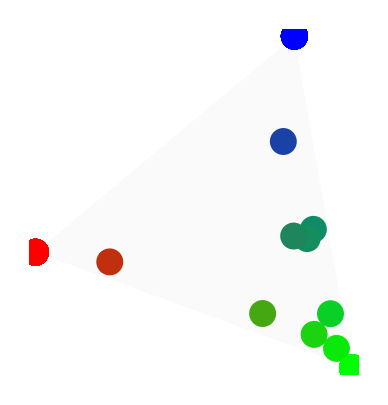

```mathematica
Show[Graphics[{Opacity[0.02],Simplex[triS1C1[[-3;;]]]},Frame->False],Graphics[Flatten[{PointSize[.05],{Blend[{Red,Blue,Green},#[[2]]],Point[#[[1]]]}&/@({triS1C1[[;;-4]],geneExpS1C1[[;;-4]]}ᵀ)}],AspectRatio->Automatic,Frame->False],PlotRange->All]
```

```mathematica
a=1;b=1;c=1;d=1;ω1=1;ω2=1;ω3=1;
resS1C2=NMaximize[{(Sum[(ⅇ^(-√((1-g1[x])^2+(g2[x])^2+(g3[x])^2)))(1-a x[[1]]),{x,cellCoordinates2D}])^ω1(Sum[(ⅇ^(-√((g1[x])^2+(1-g2[x])^2+(g3[x])^2)))(1-b x[[2]]),{x,cellCoordinates2D}])^ω2(Sum[(ⅇ^(-√((g1[x])^2+(g2[x])^2+(1-g3[x])^2))),{x,cellCoordinates2D}])^ω3
,And@@(#>0&/@Flatten[Table[{g1[x],g2[x],g3[x]},{x,cellCoordinates2D}]])(*&&And@@(#<ϵ&/@Flatten[Differences/@(Table[{g1[x],g2[x],g3[x]},{x,0,1,1/n}]ᵀ)])*)},Flatten[Table[{g1[x],g2[x],g3[x]},{x,cellCoordinates2D}]]];
```

```mathematica
resS1C2[[1]]
```

91954.5

```mathematica
triS1C2=PrincipalComponents[Join[Chop[Table[{g1[x],g2[x],g3[x]},{x,cellCoordinates2D}]/.resS1C2[[2]],10^-2],{{1,0,0},{0,1,0},{0,0,1}}]][[;;,;;2]];
```

```mathematica
geneExpS1C2=Join[Chop[Table[{g1[x],g2[x],g3[x]},{x,cellCoordinates2D}]/.resS1C2[[2]],10^-2],{{1,0,0},{0,1,0},{0,0,1}}];
```

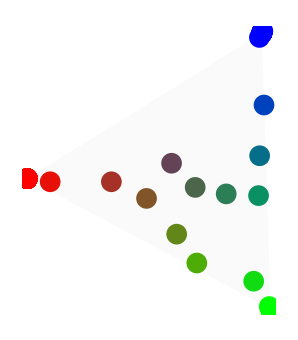

```mathematica
Show[Graphics[{Opacity[0.02],Simplex[triS1C2[[-3;;]]]},Frame->False],Graphics[Flatten[{PointSize[.05],{Blend[{Red,Blue,Green},#[[2]]],Point[#[[1]]]}&/@({triS1C2[[;;-4]],geneExpS1C2[[;;-4]]}ᵀ)}],AspectRatio->Automatic,Frame->False],PlotRange->All]
```

```mathematica
a=1;b=1;c=1;d=1;ω1=1;ω2=1;ω3=1;
resS1D1=NMaximize[{(Sum[(10-√((1-g1[x])^2+(g2[x])^2+(g3[x])^2))(0.01+x[[1]]^2/(x[[1]]^2+0.5^2)),{x,cellCoordinates2D}])^ω1(Sum[(10-√((g1[x])^2+(1-g2[x])^2+(g3[x])^2))(0.01+0.5^2/(x[[1]]^2+0.5^2)),{x,cellCoordinates2D}])^ω2(Sum[(10-√((g1[x])^2+(g2[x])^2+(1-g3[x])^2)),{x,cellCoordinates2D}])^ω3
,And@@(#>0&/@Flatten[Table[{g1[x],g2[x],g3[x]},{x,cellCoordinates2D}]])(*&&And@@(#<ϵ&/@Flatten[Differences/@(Table[{g1[x],g2[x],g3[x]},{x,0,1,1/n}]ᵀ)])*)},Flatten[Table[{g1[x],g2[x],g3[x]},{x,cellCoordinates2D}]]];
```

```mathematica
resS1D1[[1]]
```

3.65858×10^8

```mathematica
triS1D1=PrincipalComponents[Join[Chop[Table[{g1[x],g2[x],g3[x]},{x,cellCoordinates2D}]/.resS1D1[[2]],10^-2],{{1,0,0},{0,1,0},{0,0,1}}]][[;;,;;2]];
```

```mathematica
geneExpS1D1=Join[Chop[Table[{g1[x],g2[x],g3[x]},{x,cellCoordinates2D}]/.resS1D1[[2]],10^-2],{{1,0,0},{0,1,0},{0,0,1}}];
```

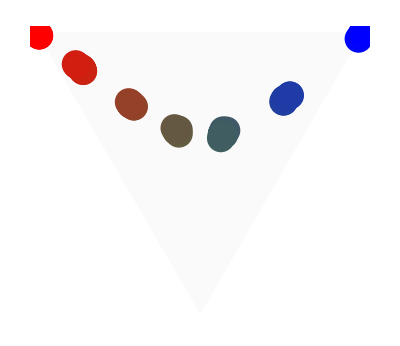

```mathematica
Show[Graphics[{Opacity[0.02],Simplex[triS1D1[[-3;;]]]},Frame->False],Graphics[Flatten[{PointSize[.05],{Blend[{Red,Blue,Green},#[[2]]],Point[#[[1]]]}&/@({triS1D1[[;;-4]],geneExpS1D1[[;;-4]]}ᵀ)}],AspectRatio->Automatic,Frame->False],PlotRange->All]
```

```mathematica
a=1;b=1;c=1;d=1;ω1=1;ω2=1;ω3=1;
resS1D2=NMaximize[{(Sum[(10-√((1-g1[x])^2+(g2[x])^2+(g3[x])^2))(0.01+0.5^2/(x[[1]]^2+0.5^2)),{x,cellCoordinates2D}])^ω1(Sum[(10-√((g1[x])^2+(1-g2[x])^2+(g3[x])^2))(0.01+0.5^2/(x[[2]]^2+0.5^2)),{x,cellCoordinates2D}])^ω2(Sum[(10-√((g1[x])^2+(g2[x])^2+(1-g3[x])^2)),{x,cellCoordinates2D}])^ω3
,And@@(#>0&/@Flatten[Table[{g1[x],g2[x],g3[x]},{x,cellCoordinates2D}]])(*&&And@@(#<ϵ&/@Flatten[Differences/@(Table[{g1[x],g2[x],g3[x]},{x,0,1,1/n}]ᵀ)])*)},Flatten[Table[{g1[x],g2[x],g3[x]},{x,cellCoordinates2D}]]];
```

```mathematica
resS1D2[[1]]
```

4.5175×10^8

```mathematica
triS1D2=PrincipalComponents[Join[Chop[Table[{g1[x],g2[x],g3[x]},{x,cellCoordinates2D}]/.resS1D2[[2]],10^-2],{{1,0,0},{0,1,0},{0,0,1}}]][[;;,;;2]];
```

```mathematica
geneExpS1D2=Join[Chop[Table[{g1[x],g2[x],g3[x]},{x,cellCoordinates2D}]/.resS1D2[[2]],10^-2],{{1,0,0},{0,1,0},{0,0,1}}];
```

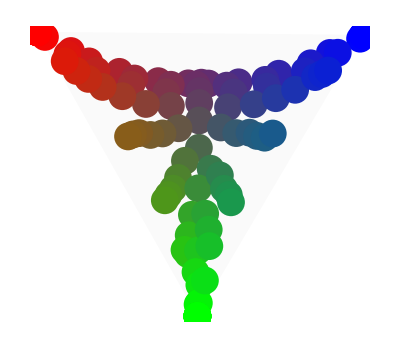

```mathematica
Show[Graphics[{Opacity[0.02],Simplex[triS1D2[[-3;;]]]},Frame->False],Graphics[Flatten[{PointSize[.05],{Blend[{Red,Blue,Green},#[[2]]],Point[#[[1]]]}&/@({triS1D2[[;;-4]],geneExpS1D2[[;;-4]]}ᵀ)}],AspectRatio->Automatic,Frame->False],PlotRange->All]
```

```mathematica
a=1;b=1;c=1;d=1;ω1=1;ω2=1;ω3=1;
resS1E1=NMaximize[{(Sum[(10-((1-g1[x])^2+(g2[x])^2+(g3[x])^2))(0.001+x[[1]]),{x,cellCoordinates2D}])^ω1+(Sum[(10-((g1[x])^2+(1-g2[x])^2+(g3[x])^2))(1-x[[1]]),{x,cellCoordinates2D}])^ω2+(Sum[(10-((g1[x])^2+(g2[x])^2+(1-g3[x])^2)),{x,cellCoordinates2D}])^ω3
,And@@(#>0&/@Flatten[Table[{g1[x],g2[x],g3[x]},{x,cellCoordinates2D}]])(*&&And@@(#<ϵ&/@Flatten[Differences/@(Table[{g1[x],g2[x],g3[x]},{x,0,1,1/n}]ᵀ)])*)},Flatten[Table[{g1[x],g2[x],g3[x]},{x,cellCoordinates2D}]]];
```

```mathematica
resS1E1[[1]]
```

2281.95

```mathematica
triS1E1=PrincipalComponents[Join[Chop[Table[{g1[x],g2[x],g3[x]},{x,cellCoordinates2D}]/.resS1E1[[2]],10^-2],{{1,0,0},{0,1,0},{0,0,1}}]][[;;,;;2]];
```

```mathematica
geneExpS1E1=Join[Chop[Table[{g1[x],g2[x],g3[x]},{x,cellCoordinates2D}]/.resS1E1[[2]],10^-2],{{1,0,0},{0,1,0},{0,0,1}}];
```

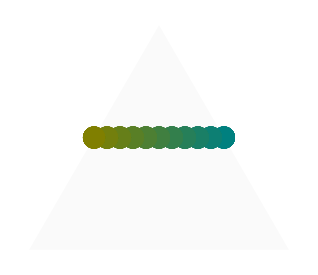

```mathematica
Show[Graphics[{Opacity[0.02],Simplex[triS1E1[[-3;;]]]},Frame->False],Graphics[Flatten[{PointSize[.05],{Blend[{Red,Blue,Green},#[[2]]],Point[#[[1]]]}&/@({triS1E1[[;;-4]],geneExpS1E1[[;;-4]]}ᵀ)}],AspectRatio->Automatic,Frame->False],PlotRange->All]
```

```mathematica
a=1;b=1;c=1;d=1;ω1=1;ω2=1;ω3=1;
resS1E2=NMaximize[{(Sum[(10-((1-g1[x])^2+(g2[x])^2+(g3[x])^2))(1-x[[2]]),{x,cellCoordinates2D}])^ω1+(Sum[(10-((g1[x])^2+(1-g2[x])^2+(g3[x])^2))(1-x[[1]]),{x,cellCoordinates2D}])^ω2+(Sum[(10-((g1[x])^2+(g2[x])^2+(1-g3[x])^2)),{x,cellCoordinates2D}])^ω3
,And@@(#>0&/@Flatten[Table[{g1[x],g2[x],g3[x]},{x,cellCoordinates2D}]])(*&&And@@(#<ϵ&/@Flatten[Differences/@(Table[{g1[x],g2[x],g3[x]},{x,0,1,1/n}]ᵀ)])*)},Flatten[Table[{g1[x],g2[x],g3[x]},{x,cellCoordinates2D}]]];
```

```mathematica
resS1E2[[1]]
```

2280.11

```mathematica
triS1E2=PrincipalComponents[Join[Chop[Table[{g1[x],g2[x],g3[x]},{x,cellCoordinates2D}]/.resS1E2[[2]],10^-2],{{1,0,0},{0,1,0},{0,0,1}}]][[;;,;;2]];
```

```mathematica
geneExpS1E2=Join[Chop[Table[{g1[x],g2[x],g3[x]},{x,cellCoordinates2D}]/.resS1E2[[2]],10^-2],{{1,0,0},{0,1,0},{0,0,1}}];
```

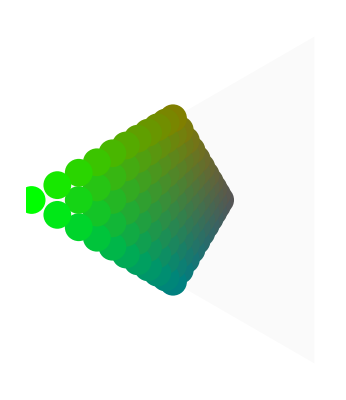

```mathematica
Show[Graphics[{Opacity[0.02],Simplex[triS1E2[[-3;;]]]},Frame->False],Graphics[Flatten[{PointSize[.05],{Blend[{Red,Blue,Green},#[[2]]],Point[#[[1]]]}&/@({triS1E2[[;;-4]],geneExpS1E2[[;;-4]]}ᵀ)}],AspectRatio->Automatic,Frame->False],PlotRange->All]
```

Figure 4

```mathematica
cellCoordinates=Flatten[Table[Append[#,z]&/@Select[Flatten[Table[{x,y},{x,0,1,1/15},{y,0,1,1/15}],1],#[[2]]+√3#[[1]]≤ √3&&#[[2]]-1/(√3)#[[1]]≤ 0&],{z,0,1,1/15}],1];
```

```mathematica
polarCellCo3D={N@√((#[[1]])^2+(#[[2]])^2),If[#[[1]]==0,0,ArcTan[N@((#[[2]])/(#[[1]]))]],#[[3]]}&/@cellCoordinates;
```

```mathematica
hexahedron=Flatten[{Line@Partition[#,2,1]&/@#,Line/@(#ᵀ)}&@Table[Append[#,i]&/@{{1,0},{1/2,(√3)/2},{-1/2,(√3)/2},{-1,0},{-1/2,-(√3)/2},{1/2,-(√3)/2},{1,0}},{i,0,1}]];
```

```mathematica
allCells=Join@@Join[
Table[Flatten[{RotationMatrix[i π/6].#[[;;2]],#[[3]]}]&/@cellCoordinates,{i,0,10,2}],
Table[Flatten[{RotationMatrix[i π/6].ReflectionMatrix[{(√3)/2,1/2}].#[[;;2]],#[[3]]}]&/@cellCoordinates,{i,0,11,2}]];
```

```mathematica
vert=Table[{Cos[θ],Sin[θ]},{θ,0,2 π-π/3,π/3}];
```

```mathematica
{Graphics3D[{{PointSize[0.05],GrayLevel[1-#[[3]]],Point[#]}&/@allCells,hexahedron},Boxed->False],
Graphics3D[{{PointSize[0.05],GrayLevel[1-Norm[#[[;;2]]]],Point[#]}&/@allCells,hexahedron},Boxed->False],Graphics3D[{{PointSize[0.05],GrayLevel[Norm[#[[;;2]]]],Point[#]}&/@allCells,hexahedron},Boxed->False],Graphics3D[{{PointSize[0.05],GrayLevel[1-E^(-3 Min[Table[EuclideanDistance[#[[;;2]],i],{i,vert}]]^2)],Point[#]}&/@allCells[[;;]],hexahedron},Boxed->False]}
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
a=1;b=1;c=1;d=1;ω1=1;ω2=1;ω3=1;ω4=1;
res4C=NMaximize[{(Sum[(10-√((1-g1[x])^2+(g2[x])^2+(g3[x])^2+(g4[x])^2))(0.01+a x[[1]]-c x[[2]]),{x,polarCellCo3D}])^ω1(Sum[(10-√((g1[x])^2+(1-g2[x])^2+(g3[x])^2+(g4[x])^2))(1-b x[[1]]),{x,polarCellCo3D}])^ω2(Sum[(10-√((g1[x])^2+(g2[x])^2+(1-g3[x])^2+(g4[x])^2))(0.01+a x[[1]]),{x,polarCellCo3D}])^ω3(Sum[(10-√((g1[x])^2+(g2[x])^2+(g3[x])^2+(1-g4[x])^2))(0.01+a x[[3]]),{x,polarCellCo3D}])^ω4
,And@@(#>0&/@Flatten[Table[{g1[x],g2[x],g3[x],g4[x]},{x,polarCellCo3D}]])(*&&And@@(#<ϵ&/@Flatten[Differences/@(Table[{g1[x],g2[x],g3[x]},{x,0,1,1/n}]ᵀ)])*)},Flatten[Table[{g1[x],g2[x],g3[x],g4[x]},{x,polarCellCo3D}]]];
```

```mathematica
tet4C=PrincipalComponents[Join[Chop[Table[{g1[x],g2[x],g3[x],g4[x]},{x,polarCellCo3D}]/.Thread[Flatten[Table[{g1[x],g2[x],g3[x],g4[x]},{x,polarCellCo3D}]]->res4C[[2]],10^-2],{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}]][[;;,;;3]];
```

```mathematica
geneExp4C=Partition[res4C[[2,;;,2]],4]
```

```mathematica
Show[Graphics3D[{Opacity[0.02],Simplex[tet4C[[-4;;]]]},Boxed->False],Graphics3D[Flatten[{PointSize[.03],{Blend[{Red,Blue,Green,Yellow},#[[2]]],Point[#[[1]]]}&/@({tet4C[[;;-5]],geneExp4C[[;;]]}ᵀ)}],AspectRatio->Automatic,Boxed->False],PlotRange->All]
```

-Graphics3D-

```mathematica
colors=Blend[{Red,Blue,Green,Yellow},#]&/@geneExp4C;
```

```mathematica
Graphics3D[{
PointSize[.03],
Join[
{colors,Point/@#}ᵀ&/@Table[Flatten[{RotationMatrix[i π/6].#[[;;2]],#[[3]]}]&/@cellCoordinates,{i,0,10,2}],
{colors,Point/@#}ᵀ&/@Table[Flatten[{RotationMatrix[i π/6].ReflectionMatrix[{(√3)/2,1/2}].#[[;;2]],#[[3]]}]&/@cellCoordinates,{i,0,11,2}]],
hexahedron},Boxed->False]
```

-Graphics3D-

```mathematica
ListLinePlot[Mean/@GatherBy[Sort[#],#[[1]]<.1|.1≤ #[[1]]<.2|.2≤#[[1]]<.3|.3≤#[[1]]<.4|.4≤#[[1]]<.5|.5≤#[[1]]<.6|.6≤#[[1]]<.7|.7≤#[[1]]<.8|.8≤#[[1]](*<.9|.9≤#[[1]]*)&]&/@Evaluate[{Table[{x[[1]],g1[x]},{x,polarCellCo3D}],Table[{x[[1]],g2[x]},{x,polarCellCo3D}],Table[{x[[1]],g3[x]},{x,polarCellCo3D}],Table[{x[[1]],g4[x]},{x,polarCellCo3D}]}/.res4C[[2]]],PlotRange->All,AxesOrigin->{0,0},Axes->False,Frame->True,FrameLabel->{"radial Axis of lobule","geneExpression"},PlotStyle->{{Thickness[.02],Red,PointSize[0.03]},{Thickness[.02],Blue,PointSize[0.03]},{Thickness[.02],Green,PointSize[0.03]},{Thickness[.02],Yellow,PointSize[0.03]}}]
```